```mathematica
n=3;
ls=Table[SeriesCoefficient[(-1)^k/k!*Log[1+ProductLog[-x]]^k*n!,{x,0,n}],{k,1,n}];
```

```mathematica
ls
```

{17,9,1}

```mathematica
mean[list_]:=Total[Table[list[[i]][[1]]*list[[i]][[2]],{i,1,Length@list}]]/((Length@list)^(Length@list))
```

```mathematica
mean@Enumerate@ls//N
```

1.40741

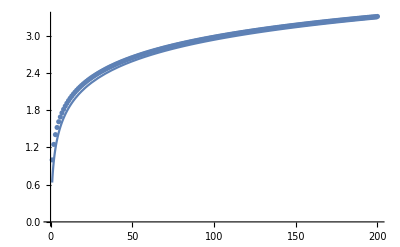

```mathematica
Show[ListPlot[ls1],Plot[(EulerGamma+Log[2])/2 +Log[x]/2,{x,1,200}]]
```

```mathematica
n=10
Sum[(k-1)!*Binomial[n,k]*n^(n-k),{k,1,n}]/n^n
```

10

59782109/31250000

```mathematica
n=100;
ls1=Table[SeriesCoefficient[-Log[1+ProductLog[-x]]/(1+ProductLog[-x]),{x,0,k}]*(k!)/k^k,{k,1,n}];
```

```mathematica
ls1
```

{1,5,38,390,5049,78960,1447886,30461872,723267369,19130274880,557794986814,17775137850624,614607897664305,22917282895782912,916671255921364950,39152092883971954688,1778431981539189344177,85607684151779322519552,4353142694568849287025142,233169669255877689516032000,13122189891443883161784728457,774098864124436347645574643712,47766530309973668256839061173502,3077147548908775964879881876537344,206585423079308733608069526411625625,14430058226740689770789738807868522496,1047123450640688990929586882322998022990,78828177844283262629133248896475305345024,6148288950831510037067977404412489383405505,496238191480193571816700537727238537216000000,41399771101521090078451746497414049985779023430,3566298238118198174817891220704775697491675840512,316896884036684908906156666229005517967213388271841,29019734026569989680621784248880410620380589049511936,2736290837341881255011697574093524617090901281422343750,265438751436829102558055827208059309052863357033994256384,26470330797472327000663606905050123036318823765672297693913,2711598461219858129925839386472569886252659064981322255564800,285139367096172189097555738300453840007193939662817743418806958,30758499597484126024721476611429584080495137393650486476800000000,3401527865307292835979404568218849130920882866259477646950731876233,385409078117039661854303666105398310934976605691728598185627095138304,44715630866256975696411872968288926713932170610211299080998871263654366,5309435267650104133543977286042665570463162447212375394302400411035762688,644854341500982039763288604181210495606338848699973496672967313171994140625,80072259051179592985152423375065953087986389832812373547498014915614948196352,10160191780430387862193500813889151690710243259641832429776324448848607451285814,1316806953299637437291627901746317756420889376431884971119070922057384231044120576,174241642164063768001327303645218523942224112882769456257968303817159507605267674001,23529269379047867345281562257016282312642600366163839950425053063861753610240000000000,3241274828423001319109594698898183802167817569153660802937546020555267523164669949017366,455308064598326213786838396585238466086913784659000634141089918250017084802577379612426240,65195032666912225713610013485051834329219366125469620523020418982498122374688967087192523177,9512333234409264893310541741275179191315320779390401285005408547631151909563933219010222489600,1413749476378709190460826735747551835720770341111361077097465807016577426723298684352343261718750,213956570460681626030053987360529042352864882607561719086293354032523442356009912061155908937318400,32961475520680944324103910779273345198640414964936195995756393401087561698602616617988470684861403129,5167499840804338580473764658093966032424702229750193458083046134419418651753355610927560656470826549248,824169827312158820551757109619092121028251278023931372260230181703095179997787079677504285297026902417134,133687057795703561196655907114250666013227018404404204109510946209488885004068058390690172764160000000000000,22048376740761369113062887962214612620205049543731519683560403094180081995963019152685080178295089803986623329,3696244083174819866285177893421453406474181354266298004693193222387074231095225150777453434010124731564693651456,629690845561912614094753225033754564676725128055507623424580437347956959979585391160919080352141708141187103320230,108984915051723890485446195964543219127469276379943399810554092653258812310143318343800791828175528762059002239516672,19158904347622092629711010242248715637473823878338810420800975811138221834527939556581323761322679322591337652587890625,3420081795234583574921310795709794327193555912487356636572534969400440255676480978641315293168664671716645361761048854528,619816692948506837656754553820212216753310041546240877918202215072168427812991968206016696236206437151909137745140188857958,114012743362208067122039627148208342639703241974481682572399764545082660490781005217514711408850049281869891558408304960995328,21281985090507188543710005377393765084593756758914034999450177607399231950315799891768192202711196639144018201862844542314532857,4030393796975309496115532211855867130386781205358067821441855700956687938759990386650901071164040474071672054349824000000000000000,774230103679668863687662210116790746020510043563651122226250939607199201089991608817745683529323945608626502245572135690520869236622,150831821560275281630411799556813702614210437503189474535222624729821934235539519007624303294406715947224819828670778871243202791211008,29794203511368242919679093303465345251515349787375697834034455877171350711941797988416490994122635844232683421726862270607311681227060713,5966289234159038405331353244950196258218206447809806185727919759496027719851228051257044475939630218759971914200073783678708201968216571904,1210962229231909826015967984020710515227620715654831265069542561730216577399995894404177420825417999107422549467083631476435329452819824218750,249076548422418678915106789621308522724569518659006257888769563282339450329371141905558405364460869091962284706218223878820362283201542525812736,51908113541797164365484392570541711184321726572564957261841179911108346418271980625244999061503066454814949119800246020964384607101386357503898225,10958825187711819206863062588368749500840855699293832755622920665530180692572097177912950803680253328337983007623773018432498719763648564159206916096,2343403998231927307434613478426969394889172026377731278712020086658405508749607781815319347172910433570287378267989427623536848649475600993892322923670,507474975608011464851656949115483754134567245187468081867813185740081437006274850484119770640864193022705829538255960848565199779659776000000000000000000,111275108114355885022815080815406758638988665178998415911304688080513854870568554687218931142218049278272746407019060179221483851875673029017989481174885745,24701917205914887231052472552892131959799236823123366508209526000754955080743651601647297541947458992930748883575067288670763048173641409009192405513397075968,5550696456309621723310364099619223813377009306759609331657721009531836211977156779289311526293799580958591833880287757684679848263876141717993234123176656048694,1262365085672004343225556137593050745712673007531259853070542734973929030344705876763061982744902084041180387979736335957077810479022394004579319103850182445367296,290523426437802602855242039484546406423249113254608863506823459242409560358548706229681616606758009670092206406853294988126126782417374341370238695270938873291015625,67651197772231742162425102740959677462374403624808351896650332865127252838363604757551207074806354749476114046323755543211952336319066798066845917285635309296653697024,15937083154599149963868528977284224843814515007841303044208423182417943179476345244162784231807252861880515463202455977589194733306235332191032685831936211732632680505022,3797724226227413239705489625711886407905717050634813579020290165772328275567712558106105294068751691738998673085579584905816026367736291771898211493949152706965075478446080,915298564429497811075905666998042740415197505785566437892146748161110699805362785371248766787058926803837616493476525532882515382387766880375507558462086148939939596025418073,223085685759185665610262908343124205354920453255285742060325493151802502605738256126905061703639355004922263225918431929085598756998324850721584789446249676800000000000000000000,54978921585678146176831899503332293130852894884243980261463172073580433720736323806227599422035081250677350706650412627141912799424703251105720824003463260536850794131017055405198,13698831447174213998082066815738423919499029838592721773598521403147061613227143270002583342505635203539324341546601991531398172898158418393268882087461644262637088713330286988886016,3450499507515223353495210398478222577803925430494293005661416629999612269320402915805383275619009620883629461925979475210913999276638307168859714355844698279706966316509262298968046849,878498486082018730848687326465960684622946251942583332922076264159883620996912251612695534153980391836654372791011063043399742344759083964127673415154800253369563316979725918962710478848,226053478998775842739014382572363927713832969210005484179965610446553217910548450966538800923638245112349238338046950362971297457993841075294438156472926531242982667897839987754821777343750,58781961312142094177116174078601648605481012433436233550614929196065091126980554414804826425018719405006229594539904256046979454741718718596251206072998062378229662016165559307023932186427392,15445153369662936066278551032956461408848960578618984643118748872508857973606362750009653219157428998843433071196459596732457173290954384737761640240421141444085392122492472023180550313531581601,4100239304300211963828536343293981145894255703308423084026922987323684307743514576150724104663998403951821309058026101539973958854309047960449293440565069571572454569749558461467191891338192748544,1099637412839001901044550827652809690201449960623561729798620056814113181779817769214924020939118981128880397691554821176998284370562325771008574323071148847574553052599317610228253055944839209490566,297898659096572482780267626128211410466510042279181478450257766231133156491806795252630595532564926575425193987578038347001313290059763689763176736746310894866907980151579622768640000000000000000000000}

```mathematica
ProductLog[0]
```

0

```mathematica
Clear@n
```

```mathematica
D[ProductLog[x],{x,n}]
```

ProductLog^(n)[x]

```mathematica
Series[Log[1+x],{x,0,10}]
```

x-x^2/2+x^3/3-x^4/4+x^5/5-x^6/6+x^7/7-x^8/8+x^9/9-x^10/10+O[x]^11

```mathematica
Series[1/(1+x),{x,0,10}]
```

1-x+x^2-x^3+x^4-x^5+x^6-x^7+x^8-x^9+x^10+O[x]^11

```mathematica
D[Log[1+ProductLog[-x]]/(1+ProductLog[-x]),{x,1}]//Expand
```

ProductLog[-x]/(x (1+ProductLog[-x])^3)-(Log[1+ProductLog[-x]] ProductLog[-x])/(x (1+ProductLog[-x])^3)

```mathematica
ls[[1]]
```

12209960630215980300253132956815012998412714159392662223854992521128809374822896606879062793565756480077431168694642794552798934366694577253573013735421843845957043306726309232640000000000000000000000